```mathematica
(* Simple example case where alpha is a constant = pi/2, no z derivatives:

s = NDSolve[{K*((u^3)*D[phi[u],u]+D[phi[u],u,u]*(u^4)+(1/2)*(u^2)*Sin[2*phi[u]])==0,phi[.001]==0,(D[phi[u],u]/.u->.001)==.001},phi,{u,10,.001}];
Plot[Evaluate[phi[u]/.s],{u,10,.001},PlotRange->All] 

*)
```

2.84831×10^-30

NDSolve::ndsz: At u == 1., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1.00018} lies outside the range of data in the interpolating function. Extrapolation will be used.

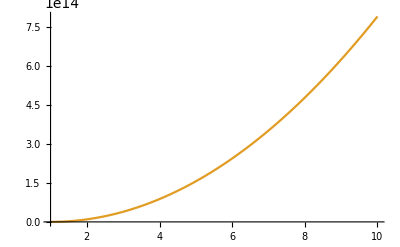

InterpolatingFunction::dmval: Input value {1.00018} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
K  =(10^(-15))*(7*10^(-5))*(.0125^4)/600
a = π/15; (* in radians! *)
lambda[a_] := ((Tan[a]^2 ) +1)/(1-(Tan[a])^2)

(*s = NDSolve[{K*((u^4)*D[phi[u],u]+D[phi[u],u,u]*(u^5)+(1/2)*(u^3)*Sin[2*phi[u]]*(Sin[alpha[u]]^2)-Sin[phi[u]]*Cos[phi[u]]*(u^5)*(D[alpha[u],u])^2)+(lambda[a]/4)*Sin[2*alpha[u]]*Sin[2*phi[u]]==0,K*((Sin[2*phi[u]])*(u^4)*D[alpha[u],u]*D[phi[u],u]+(Sin[phi[u]]^2)*(u^4)*D[alpha[u],u]+(Sin[phi[u]]^2)*(u^5)*D[alpha[u],u,u]+(1/2)*(u^3)*Sin[2*alpha[u]]*(Sin[phi[u]])^2) +(1/2)*(lambda[a]*Cos[2*alpha[u]]-1)*(Sin[phi[u]]^2)==0,(D[phi[u],u]/.u->10)==0,(D[phi[u],u]/.u->1)==0,(D[alpha[u],u]/.u->1)==0,(D[alpha[u],u]/.u->10)==0},{phi,alpha},{u,10,1}] 
Plot[Evaluate[{phi[u],alpha[u]}/.s, {u,10,1}],PlotRange -> All]
Plot[Evaluate[phi[u]/.s,{u,1.1,1}]];*)
s = NDSolve[{K*((u^4)*D[phi[u],u]+D[phi[u],u,u]*(u^5)+(1/2)*(u^3)*Sin[2*phi[u]]*(Sin[alpha[u]]^2)-Sin[phi[u]]*Cos[phi[u]]*(u^5)*(D[alpha[u],u])^2)+(lambda[a]/4)*Sin[2*alpha[u]]*Sin[2*phi[u]]==0,K*((Sin[2*phi[u]])*(u^4)*D[alpha[u],u]*D[phi[u],u]+(Sin[phi[u]]^2)*(u^4)*D[alpha[u],u]+(Sin[phi[u]]^2)*(u^5)*D[alpha[u],u,u]+(1/2)*(u^3)*Sin[2*alpha[u]]*(Sin[phi[u]])^2) +(1/2)*(lambda[a]*Cos[2*alpha[u]]-1)*(Sin[phi[u]]^2)==0,phi[1]==1,(D[phi[u],u]/.u->1)==0,(D[alpha[u],u]/.u->1)==0,alpha[1]==a},{phi,alpha},{u,10,1}] ;
Plot[Evaluate[{phi[u],alpha[u]}/.s, {u,10,1}],PlotRange -> All]
Plot[Evaluate[phi[u]/.s,{u,10,1}]];
```